## Execute this

### Loading

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
polar1bt=Import["data/densityalpha1/polarValArray_b2t.mx"];
polar1tb=Import["data/densityalpha1/polarValArray_t2b.mx"];
nematic1bt=Import["data/densityalpha1/nematicValArray_b2t.mx"];
nematic1tb=Import["data/densityalpha1/nematicValArray_t2b.mx"];
```

```mathematica
polar2bt=Import["data/densityalpha2/polarValArray_b2t.mx"];
polar2tb=Import["data/densityalpha2/polarValArray_t2b.mx"];
nematic2bt=Import["data/densityalpha2/nematicValArray_b2t.mx"];
nematic2tb=Import["data/densityalpha2/nematicValArray_t2b.mx"];;
```

```mathematica
Table[polar1bt[[;;,i,1]]=Range[0,0.75,0.03]/0.12;,{i,Length@polar1bt[[1]]}];
Table[polar1tb[[;;,i,1]]=Range[0,0.75,0.03]/0.12;,{i,Length@polar1tb[[1]]}];
Table[nematic1bt[[;;,i,1]]=Range[0,0.75,0.03]/0.12;,{i,Length@nematic1bt[[1]]}];
Table[nematic1tb[[;;,i,1]]=Range[0,0.75,0.03]/0.12;,{i,Length@nematic1tb[[1]]}];
```

```mathematica
Table[polar2bt[[;;,i,1]]=Range[0,0.75,0.015]/0.12;,{i,Length@polar2bt[[1]]}];
Table[polar2tb[[;;,i,1]]=Range[0,0.75,0.015]/0.12;,{i,Length@polar2tb[[1]]}];
Table[nematic2bt[[;;,i,1]]=Range[0,0.75,0.015]/0.12;,{i,Length@nematic2bt[[1]]}];
Table[nematic2tb[[;;,i,1]]=Range[0,0.75,0.015]/0.12;,{i,Length@nematic2tb[[1]]}];
```

```mathematica
rho1=polar1bt[[1,;;,2]]/512.^2*1000;
rho1ls=rho1*6.3^2;
rho2=polar2bt[[1,;;,2]]/512.^2*1000;
rho2ls=rho2*6.3^2;
```

```mathematica
Table[polar1bt[[i,;;,2]]=rho1ls;,{i,Length@polar1bt}];
Table[polar1tb[[i,;;,2]]=rho1ls;,{i,Length@polar1tb}];
Table[nematic1bt[[i,;;,2]]=rho1ls;,{i,Length@nematic1bt}];
Table[nematic1tb[[i,;;,2]]=rho1ls;,{i,Length@nematic1tb}];
```

```mathematica
Table[polar2bt[[i,;;,2]]=rho2ls;,{i,Length@polar2bt}];
Table[polar2tb[[i,;;,2]]=rho2ls;,{i,Length@polar2tb}];
Table[nematic2bt[[i,;;,2]]=rho2ls;,{i,Length@nematic2bt}];
Table[nematic2tb[[i,;;,2]]=rho2ls;,{i,Length@nematic2tb}];
```

```mathematica
deltaPrho=Flatten[polar2bt,1];
tempPLUS=Flatten[polar2bt,1];
tempMINUS=Flatten[polar2tb,1];
Table[deltaPrho[[i,3]]=tempPLUS[[i,3]]-tempMINUS[[i,3]],{i,1,Length@deltaPrho}];
```

### Plotting

individual sweeps

```mathematica
min=-0.0;
max=1.0;
colormap={"DeepSeaColors","Reverse"};
colfunc=ColorData[colormap][#/max]&;
legPPLUS=BarLegend[{colfunc,{min,max}},LegendLabel->"P_+"];
legPMINUS=BarLegend[{colfunc,{min,max}},LegendLabel->"P_-"];
legNPLUS=BarLegend[{colfunc,{min,max}},LegendLabel->"N_+"];
legNMINUS=BarLegend[{colfunc,{min,max}},LegendLabel->"N_-"];
polplotbt=Show[{ListDensityPlot[Flatten[polar1bt,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->legPPLUS,FrameLabel->{"α","ρL^2"}],ListDensityPlot[Flatten[polar2bt,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False]}];
polplottb=Show[{ListDensityPlot[Flatten[polar1tb,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->legPMINUS,FrameLabel->{"α","ρL^2"}],ListDensityPlot[Flatten[polar2tb,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False]}];
nemplotbt=Show[{ListDensityPlot[Flatten[nematic1bt,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->legNPLUS,FrameLabel->{"α","ρL^2"}],ListDensityPlot[Flatten[nematic2bt,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False]}];
nemplottb=Show[{ListDensityPlot[Flatten[nematic1tb,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->legNMINUS,FrameLabel->{"α","ρL^2"}],ListDensityPlot[Flatten[nematic2tb,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False]}];
GraphicsRow[{polplotbt,polplottb},ImageSize->600]
GraphicsRow[{nemplotbt,nemplottb},ImageSize->600]
```

-Graphics-

-Graphics-

hysteresis

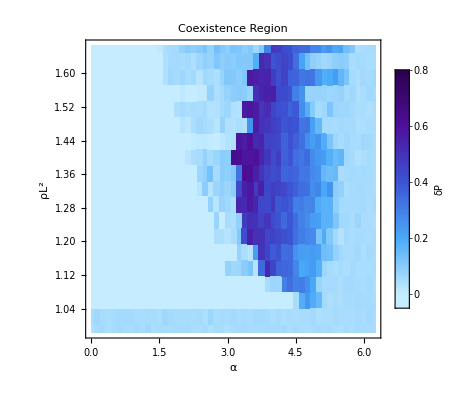

```mathematica
min=-0.05;
max=0.8;
colormap={"DeepSeaColors","Reverse"};
colfunc=ColorData[colormap][#/max]&;
leg=BarLegend[{colfunc,{min,max}},LegendLabel->"δP"];
ListDensityPlot[deltaPrho,InterpolationOrder->0,PlotLabel->Style["Coexistence Region",14],PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->leg,FrameLabel->{"α","ρL^2"}]
```